```mathematica
Clear[wzx,μx,berryPhoton,berryAtomic,EN,ES]
wzx [nx_,nz_]:= wo √(1-(nz-nx)/wo);
μx[nx_,nz_,q_] := 1/(wzx[nx,nz]^2/wo^2*(q^2-1)+1);
EN[nz_]:=-1+nz/(2*wo);
ES[nx_,nz_,q_]:=-1/2*(μx[nx,nz,q]+1/μx[nx,nz,q])+nz/(2*wo);
berryPhoton [nx_,nz_,q_]:= Pi/2*q^2*(1-μx[nx,nz,q]^2)/wo*wzx [nx,nz]^2;
berryAtomic[nx_,nz_,q_]:=Pi*(1-μx[nx,nz,q]);
```

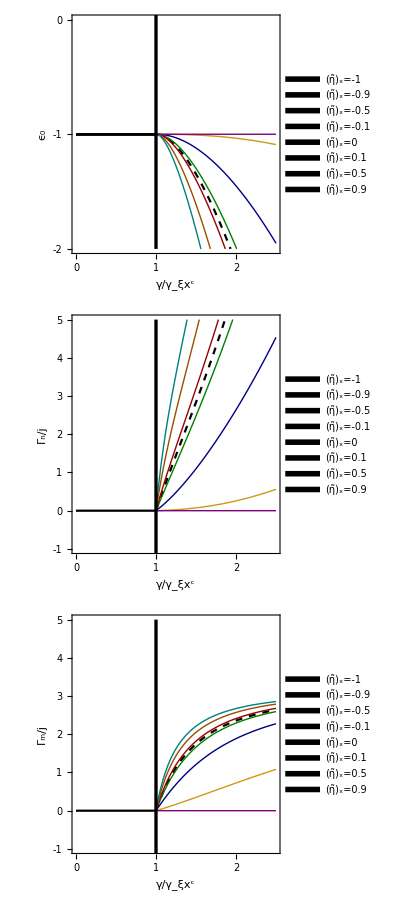

```mathematica
Clear[AxeX,AxeY,scale, color1,color2,color3,color4,color5,color6,color7,color8,align]
AxeX=2.5;
AxeY=5;
scale=600;
align[Center]={0,0};  
(*color1=Black; color2=Green; color3=Blue;color4=RGBColor[1,0.75,0]; color5=Orange; color6=Purple; color7=RGBColor[0,0.8,0.8];color8=RGBColor[0.6,0.3,0];*)
color1=Black;
color2=RGBColor[0,0.5,0]; (*Verde Oscuro*)
color3=RGBColor[0,0,0.5]; (*Azul Marino*)
color4=RGBColor[0.8,0.6,0.1]; (*Ocre*)
color5=RGBColor[0.6,0,0]; (*Rojo Oscuro*)
color6=RGBColor[0.6,0.3,0]; (*Marrón*)
color7=RGBColor[0,0.5,0.5]; (*Cian Oscuro*)
color8=RGBColor[0.5,0,0.5]; (*Morado Oscuro*)

(* Energy *)
Clear[x1E,y1E]
x1E=0.5; y1E=-1.3;
Clear[Da,Th]
Da=Dashed;
Th=Thick;

Clear[PEnergyN,PEnergyS]
PEnergyN[nz_,colorLine_]:=Plot[EN[nz],{q,0,1},PlotStyle->colorLine];
PEnergyS[nx_,nz_,colorLine_,x1_,y1_,line_]:=Plot[ES[nx,nz,q],{q,1,AxeX},Frame->True,PlotRange->{{0,AxeX},{-2,0}},
FrameTicksStyle->{Directive[Black,FontSize->20],Directive[Transparent,FontSize->20]},
FrameLabel->{Style["γ/γ_ξx^c",FontSize->3,Transparent],Style["ϵ_0",FontSize->35,Black]},
PlotStyle->{line,colorLine},
ImageSize->600,
FrameTicks->{{{-2,-1,0},None},{{0,0.5,1,1.5,2,2.5},None}},
Epilog->{Thickness[0.004],{Line[{{1,-2},{1,AxeY}}]},
Inset[SwatchLegend[{color8},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{-0.08+x1,y1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color4},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.9]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-0.2},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color3},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.5]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-0.4},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color2},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-0.6},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color1},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{-0.08+x1+0.5,y1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color5},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-0.2},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color6},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.5]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-0.4},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color7},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.9]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-0.6},{Right,Bottom},Scaled[{0.3,0.3}]]

}];
Clear[plotsEnergy]
plotsEnergy=Show[PEnergyS[0,0,color1,x1E,y1E,Da],PEnergyN[0,color1],PEnergyS[-0.1,0,color2,x1E,y1E,Th],PEnergyN[0,color2],PEnergyS[-0.5,0,color3,x1E,y1E,Th],PEnergyN[0,color3],PEnergyS[-0.9,0,color4,x1E,y1E,Th],PEnergyN[0,color4],PEnergyS[0.1,0,color5,x1E,y1E,Th],PEnergyN[0,Black],PEnergyS[0.5,0,color6,x1E,y1E,Th],PEnergyN[0,Black],PEnergyS[0.9,0,color7,x1E,y1E,Th],PEnergyN[0,Black],PEnergyS[-1,0,color8,x1E,y1E,Th],PEnergyN[0,Black]];


(* Photon *)
Clear[x1P,y1P]
x1P=0.5;  y1P=1.9;
Clear[PPhotonN,PPhotonS]
PPhotonN=Plot[0,{q,0,1},PlotStyle->Black];
PPhotonS[nx_,nz_,colorLine_,x1_,y1_,line_]:=Plot[berryPhoton[nx,nz,q],{q,1,AxeX},Frame->True,PlotRange->{{0,AxeX},{-1,AxeY}},
FrameTicksStyle->{Directive[Black,FontSize->20]
,Directive[Transparent,FontSize->20]},
FrameTicks->{{{-1,0,1,2,3,4,5},None},{{0,0.5,1,1.5,2,2.5},None}},
FrameLabel->{Style["γ/γ_ξx^c",FontSize->3,Transparent],Style["Γ_n/j",FontSize->35,Black]},
PlotStyle->{line,colorLine},
ImageSize->scale,Epilog->{Thickness[0.004],{Line[{{1,-2},{1,AxeY}}]},
Inset[SwatchLegend[{color8},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{-0.08+x1,y1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color4},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.9]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-0.5},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color3},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.5]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color2},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-1.5},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color1},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{-0.08+x1+0.5,y1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color5},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-0.5},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color6},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.5]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color7},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.9]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-1.5},{Right,Bottom},Scaled[{0.3,0.3}]]
}];
Clear[plotsPhoton]
plotsPhoton=Show[PPhotonS[0,0,color1,x1P,y1P,Da],PPhotonS[-0.1,0,color2,x1P,y1P,Th],PPhotonS[-0.5,0,color3,x1P,y1P,Th],PPhotonS[-0.9,0,color4,x1P,y1P,Th],PPhotonS[0.1,0,color5,x1P,y1P,Th],PPhotonS[0.5,0,color6,x1P,y1P,Th],PPhotonS[0.9,0,color7,x1P,y1P,Th],PPhotonS[-1,0,color8,x1P,y1P,Th],PPhotonN];

(* Atomic *)
Clear[x1A,y1A]
x1A=0.5; y1A=1.9;
Clear[PAtomicN,PAtomicS]
PAtomicN=Plot[0,{q,0,1},PlotStyle->Black];
PAtomicS[nx_,nz_,colorLine_,x1_,y1_,line_]:=Plot[berryAtomic[nx,nz,q],{q,1,AxeX},Frame->True,PlotRange->{{0,AxeX},{-1,AxeY}},
FrameTicksStyle->{Directive[Black,FontSize->20]
,Directive[Black,FontSize->20]},
FrameTicks->{{{-1,0,1,2,3,4,5},None},{{0,0.5,1,1.5,2,2.5},None}},
FrameLabel->{Style["γ/γ_ξx^c",FontSize->35,Black],Style["Γ_m/j",FontSize->35,Black]},
PlotStyle->{line,colorLine},
ImageSize->scale,
Epilog->{Thickness[0.004],{Line[{{1,-2},{1,AxeY}}]},
Inset[SwatchLegend[{color8},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{-0.08+x1,y1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color4},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.9]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-0.5},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color3},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.5]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color2},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[-0.1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1,y1-1.5},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color1},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{-0.08+x1+0.5,y1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color5},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.1]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-0.5},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color6},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.5]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-1},{Right,Bottom},Scaled[{0.3,0.3}]],
Inset[SwatchLegend[{color7},{Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[0.9]]},LegendMarkers->{Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LabelStyle->{FontSize->20}],{x1+0.5,y1-1.5},{Right,Bottom},Scaled[{0.3,0.3}]]
}];
Clear[plotsAtomic]
plotsAtomic=Show[PAtomicS[0,0,color1,x1A,y1A,Da],PAtomicS[-0.1,0,color2,x1A,y1A,Th],PAtomicS[-0.5,0,color3,x1A,y1A,Th],PAtomicS[-0.9,0,color4,x1A,y1A,Th],PAtomicS[0.1,0,color5,x1A,y1A,Th],PAtomicS[0.5,0,color6,x1A,y1A,Th],PAtomicS[0.9,0,color7,x1A,y1A,Th],PAtomicS[-1,0,color8,x1A,y1A,Th],PAtomicN];

SetDirectory["/Users/rich/Documentos/07 Trimestre/Entropy Campo Medio/Berry_Phase"];
exp=Grid[{{plotsEnergy},{plotsPhoton},{plotsAtomic}},Spacings->{1,0.008}]
Export["berry_phase.pdf",exp,ImageSize-> 2000,"CompressionLevel"->0,Background->White];
```